# FPGA data 2/2/2022

Data  every 1.9ms Az        Ax     Ay      dpz    dpy   dpx     wz   wy
time
1x1.9ms | ch0 | ch1 | ch2 | ch3 | ch4 | ch5 | ch6 | ch7
t | Az | Ax | Ay | dpz | dpy | dpx | wz | wy
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9	
Where Ax is the + longitudinal axis forward

Data  every 1.9ms Az        Ax     Ay      dpz    dpy   dpx     wz   wy

ch0 | ch1 | ch2 | ch3 | ch4 | ch5 | ch6 | ch7
Az | Ax | Ay | dpz | dpy | dpx | wz | wy
	
Where Ax is the + longitudinal axis forward

Logs History without Disk contact
-Graphics-

## Get the data recording .dat

for Read to work, the data should be space separated and must not have a .txt extension (use .dat)

#### find the file

```mathematica
currentDirectory = NotebookDirectory[]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\

```mathematica
datafile = SystemDialogInput["FileOpen"]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215182.dat

```mathematica
filedata =Import[datafile];
Print["Dimensions of filedata",Dimensions[filedata]];
lastrecord = Length[filedata];
d ={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]}&/@filedata;
d[[1]]
```

Dimensions of filedata{1024,9}

{0,1555,1338,1626,2742,2723,2731,2239,2230}

### Show data

```mathematica
begin = 1;end =lastrecord;
d = Take[d,{begin,If[end > lastrecord,lastrecord,end]}];
npoints= Length[d]
```

1024

Extracting time is not really required for a sequenced list with integral ordinates..this is a vestige of an earlier notebook

```mathematica
t = Map[Part[#,1]&,d];
```

```mathematica
td = {MapThread[List,{t,Map[Part[#,2]&,d]}],MapThread[List,{t,Map[Part[#,3]&,d]}],MapThread[List,{t,Map[Part[#,4]&,d]}],MapThread[List,{t,Map[Part[#,5]&,d]}],MapThread[List,{t,Map[Part[#,6]&,d]}],MapThread[List,{t,Map[Part[#,7]&,d]}],MapThread[List,{t,Map[Part[#,8]&,d]}],MapThread[List,{t,Map[Part[#,9]&,d]}]};
```

#### Plot data Az Ax Ay dpz dpy dpx wz wy

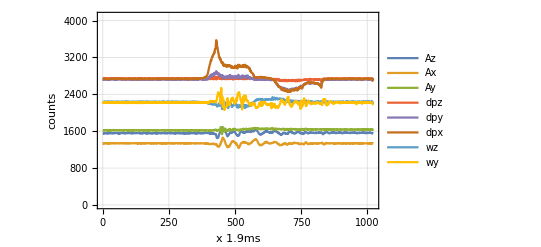

```mathematica
ListLinePlot[td,PlotLegends->{"Az","Ax","Ay","dpz","dpy","dpx","wz","wy"},Frame->True,PlotRange->{Automatic,{0,4096}},FrameLabel->{"x 1.9ms ","counts"},GridLines->Automatic]
```

#### Find the sensor means with no disturbance

```mathematica
m = {Mean[#[[1]]&/@d],Mean[#[[2]]&/@d],Mean[#[[3]]&/@d],Mean[#[[4]]&/@d],Mean[#[[5]]&/@d],Mean[#[[6]]&/@d],Mean[#[[7]]&/@d],Mean[#[[8]]&/@d],Mean[#[[9]]&/@d]}//N
```

{511.5,1563.51,1335.84,1630.64,2735.8,2706.6,2762.42,2231.83,2221.06}

#### Calculate standard deviations

putting a dummy value into [[1]] which is the ordinate.  this keeps the part indices aligned

```mathematica
sd={1,Sqrt[(#[[2]]-m[[2]]&/@d ). (#[[2]]-m[[2]]&/@d )],
Sqrt[(#[[3]]-m[[3]]&/@d ). (#[[3]]-m[[3]]&/@d )],Sqrt[(#[[4]]-m[[4]]&/@d ). (#[[4]]-m[[4]]&/@d )],Sqrt[(#[[5]]-m[[5]]&/@d ). (#[[5]]-m[[5]]&/@d )],
Sqrt[(#[[6]]-m[[6]]&/@d ). (#[[6]]-m[[6]]&/@d )],
Sqrt[(#[[7]]-m[[7]]&/@d ). (#[[7]]-m[[7]]&/@d )],
Sqrt[(#[[8]]-m[[8]]&/@d ). (#[[8]]-m[[8]]&/@d )],
Sqrt[(#[[9]]-m[[9]]&/@d ). (#[[9]]-m[[9]]&/@d )]}
```

{1,738.293,719.648,464.576,477.747,2271.14,5225.74,1170.26,1533.95}

#### Correlate Az and Ax , Wy WZ, and Px, Py

Ay and Pz are ommitted because they are not significant signals compared to the other 6

```mathematica
corrA = npoints((#[[2]]-m[[2]]&/@d )(#[[3]]-m[[3]]&/@d) )/(sd[[2]] sd[[3]] );
```

```mathematica
corrW = npoints((#[[9]]-m[[9]]&/@d )(#[[8]]-m[[8]]&/@d ))/(sd[[9]] sd[[8]]);
```

```mathematica
corrP =npoints((#[[6]]-m[[6]]&/@d )(#[[7]]-m[[7]]&/@d))/(sd[[6]] sd[[7]]);
```

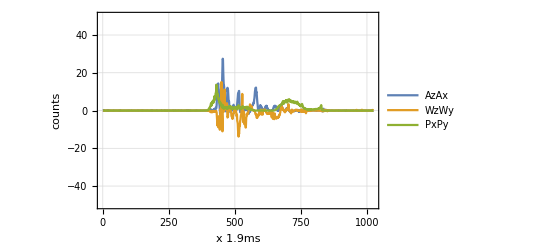

```mathematica
ListLinePlot[{corrA, corrW,corrP}, PlotLegends -> {"AzAx","WzWy", "PxPy"}, Frame -> True, PlotRange -> 
{-50, 50}, FrameLabel -> {"x 1.9ms ", "counts"}, GridLines -> Automatic]
```

### Correlate All omits the pressure precursor

```mathematica
corrAll=corrA corrW corrP ;
```

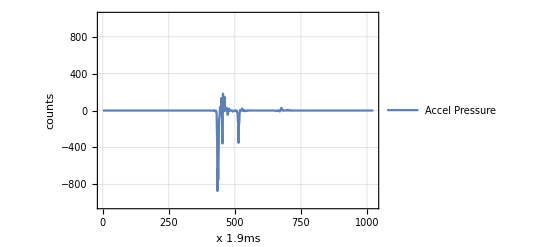

```mathematica
ListLinePlot[corrAll, PlotLegends -> {"Accel Pressure "}, Frame -> True, PlotRange -> 
{-npoints, npoints}, FrameLabel -> {"x 1.9ms ", "counts"}, GridLines -> Automatic]
```

### Construct a function to create a correlation plot

Assign means and statistics based on our  data C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215182.dat

```mathematica
m = {511.5,1563.5126953125,1335.837890625,1630.64453125,2735.802734375,2706.5966796875,2762.4169921875,2231.8291015625,2221.0556640625};
sd = {1,738.2925131415985,719.6478929613774,464.5757305058025,477.74695430086206,2271.1442994030426,5225.73678483101,1170.2568490606827,1533.9523549147273};
```

```mathematica
showfile[file_,statisticsQ_]:=Block[{},If[StringQ[file],datafile = file,datafile = SystemDialogInput["FileOpen"]];
Print[datafile];
filedata =Import[datafile];
lastrecord = Length[filedata];
d ={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]}&/@filedata;
npoints= Length[d];
t = Map[Part[#,1]&,d];
td = {MapThread[List,{t,Map[Part[#,2]&,d]}],MapThread[List,{t,Map[Part[#,3]&,d]}],MapThread[List,{t,Map[Part[#,4]&,d]}],MapThread[List,{t,Map[Part[#,5]&,d]}],MapThread[List,{t,Map[Part[#,6]&,d]}],MapThread[List,{t,Map[Part[#,7]&,d]}],MapThread[List,{t,Map[Part[#,8]&,d]}],MapThread[List,{t,Map[Part[#,9]&,d]}]};
If[statisticsQ,
m = {Mean[#[[1]]&/@d],Mean[#[[2]]&/@d],Mean[#[[3]]&/@d],Mean[#[[4]]&/@d],Mean[#[[5]]&/@d],Mean[#[[6]]&/@d],Mean[#[[7]]&/@d],Mean[#[[8]]&/@d],Mean[#[[9]]&/@d]}//N;
sd={1,Sqrt[(#[[2]]-m[[2]]&/@d ). (#[[2]]-m[[2]]&/@d )],
Sqrt[(#[[3]]-m[[3]]&/@d ). (#[[3]]-m[[3]]&/@d )],Sqrt[(#[[4]]-m[[4]]&/@d ). (#[[4]]-m[[4]]&/@d )],Sqrt[(#[[5]]-m[[5]]&/@d ). (#[[5]]-m[[5]]&/@d )],
Sqrt[(#[[6]]-m[[6]]&/@d ). (#[[6]]-m[[6]]&/@d )],
Sqrt[(#[[7]]-m[[7]]&/@d ). (#[[7]]-m[[7]]&/@d )],
Sqrt[(#[[8]]-m[[8]]&/@d ). (#[[8]]-m[[8]]&/@d )],
Sqrt[(#[[9]]-m[[9]]&/@d ). (#[[9]]-m[[9]]&/@d )]};
Print["Means m recalculated: ",m];
Print["Standard Deviations recalculated: ",sd];
];
corrA = npoints((#[[2]]-m[[2]]&/@d )(#[[3]]-m[[3]]&/@d) )/(sd[[2]] sd[[3]] );
corrW = npoints((#[[9]]-m[[9]]&/@d )(#[[8]]-m[[8]]&/@d ))/(sd[[9]] sd[[8]]);
corrP =npoints((#[[6]]-m[[6]]&/@d )(#[[7]]-m[[7]]&/@d))/(sd[[6]] sd[[7]]);
GraphicsGrid[{{ListLinePlot[td,PlotLegends->{"Az","Ax","Ay","dpz","dpy","dpx","wz","wy"},Frame->True,PlotRange->{Automatic,{0,4096}},FrameLabel->{"x 1.9ms ","counts"},GridLines->Automatic,ImageSize->400]},{ListLinePlot[{corrA,corrW,corrP},PlotLegends->{"AzAx","WzWy","PxPy"},Frame->True,PlotRange->{-50,50},FrameLabel->{"x 1.9ms ","counts"},GridLines->Automatic,ImageSize->400]}},ImageSize->Large]]
```

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c20221215182.dat",True]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215182.dat

Means m recalculated: {511.5,1563.51,1335.84,1630.64,2735.8,2706.6,2762.42,2231.83,2221.06}

Standard Deviations recalculated: {1,738.293,719.648,464.576,477.747,2271.14,5225.74,1170.26,1533.95}

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c20221215170.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215170.dat

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212151614.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212151614.dat

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c20221215155.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215155.dat

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212151356.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212151356.dat

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212151243.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212151243.dat

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212151049.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212151049.dat

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c2022121536.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c2022121536.dat

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c2022121501.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c2022121501.dat

-Graphics-

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212145827.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212145827.dat

-Graphics-

#### Create a Target - Choose a Bad Case i.e. easy to spot, with a steep pressure rise

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215182.dat

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c20221215182.dat",False]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215182.dat

-Graphics-

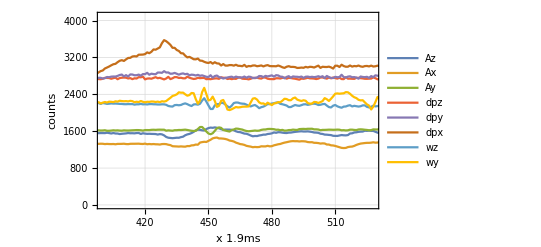

```mathematica
tstart=400;trange={tstart,tstart+128};ListLinePlot[td,
PlotLegends->{"Az","Ax","Ay","dpz","dpy","dpx","wz","wy"},Frame->True,PlotRange->{trange,{0,4096}},FrameLabel->{"x 1.9ms ","counts"},GridLines->Automatic]
```

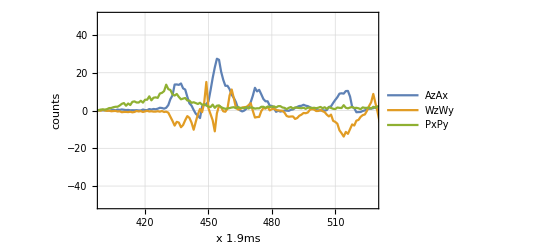

```mathematica
ListLinePlot[{corrA,corrW,corrP},PlotLegends->{"AzAx","WzWy","PxPy"},Frame->True,PlotRange->{trange,{-50,50}},FrameLabel->{"x 1.9ms ","counts"},GridLines->Automatic,ImageSize->400]
```

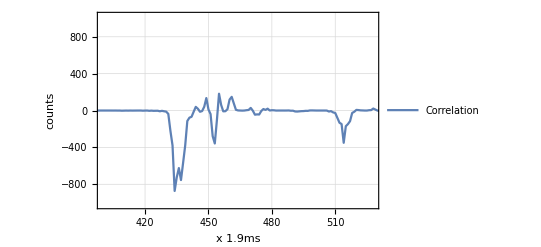

```mathematica
corrAll=corrA corrW corrP;ListLinePlot[corrAll, PlotLegends -> {"Correlation "}, Frame -> True, PlotRange ->{ trange,
{-npoints, npoints}}, FrameLabel -> {"x 1.9ms ", "counts"}, GridLines -> Automatic]
```

Look for growth over 16 frames (fifo depth 128) as a target

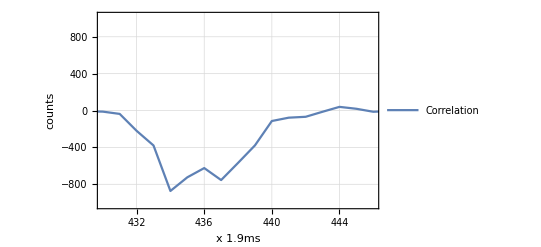

```mathematica
targetstart=430;targetrange={targetstart,targetstart+16};ListLinePlot[corrAll, PlotLegends -> {"Correlation "}, Frame -> True, PlotRange ->{ targetrange,
{-npoints, npoints}}, FrameLabel -> {"x 1.9ms ", "counts"}, GridLines -> Automatic]
```

```mathematica
target=Take[corrAll,targetrange]
```

{-11.8572,-36.6111,-220.04,-378.985,-872.428,-724.41,-624.074,-754.171,-568.152,-378.159,-113.607,-77.499,-67.9118,-13.2476,39.7259,18.9934,-13.3336}

```mathematica
target16ms = {-11.8572206745986,-24.0,-36.6110594001744,-128.0,-220.03957479173678,-299.0,-378.98450488681516,-625.0,-872.4284701299456,-798.0,-724.4098120021955,-674.0,-624.0738696341638,-689.0,-754.1710309574621,-661.0}
```

{-11.8572,-24.,-36.6111,-128.,-220.04,-299.,-378.985,-625.,-872.428,-798.,-724.41,-674.,-624.074,-689.,-754.171,-661.}

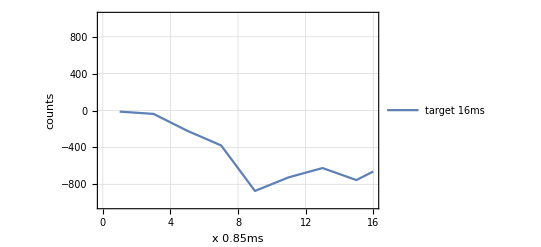

```mathematica
ListLinePlot[target16ms, PlotLegends -> {"target 16ms "}, Frame -> True, PlotRange ->{ Automatic,
{-npoints, npoints}}, FrameLabel -> {"x 0.85ms ", "counts"}, GridLines -> Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"target.dat",target,"Text"]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\target.dat

### Correlate the target with the data from c20221215182.dat as “BAD” hazardous upset

Do a running product-summation from target[[1]] to target[[16]], and then a separate on from target[[1]] to target[[5]]

```mathematica
showfile["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c20221215182.dat",False];
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215182.dat

```mathematica
crosscorr16 ={}; Do[cc=0;
(*20480 was added here, to keep scaling after removing npoints dependency from corrA, corrW, corrP*)
Do[cc = cc+ 20480target[[j]]*corrAll[[i+j]];,{j,1,16}];
AppendTo[crosscorr16,cc],
{i,1,Length[corrAll]-Length[target]}];

crosscorr5 ={}; Do[cc=0;
(*20480 was added here, to keep scaling after removing npoints dependency from corrA, corrW, corrP*)
Do[cc = cc+ 20480target[[j]]*corrAll[[i+j]];,{j,1,5}];
AppendTo[crosscorr5,cc],
{i,1,Length[corrAll]-Length[target]}];
```

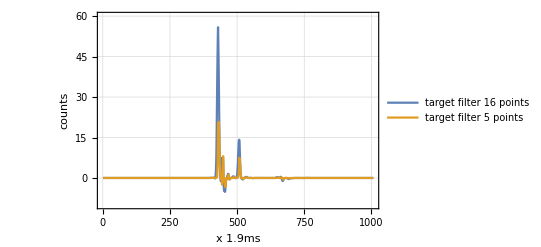

```mathematica
ListLinePlot[{crosscorr16,crosscorr5},PlotLegends -> {"target filter\n16 points","target filter\n5 points"},PlotRange->{-10, 60}, FrameLabel -> {"x 1.9ms ", "counts"}, GridLines -> Automatic, Frame -> True]
```

```mathematica
tf = ListLinePlot[{100crosscorr16,100crosscorr5},PlotLegends -> {"target filter\n16 points","target filter\n5 points"},PlotRange->{0, 4096}, FrameLabel -> {"x 1.9ms ", "counts"}, GridLines -> Automatic, Frame -> True];
```

Add the target filter 5 points to the channel plot

```mathematica
raw =ListLinePlot[{td[[1]],td[[2]],td[[5]],td[[6]],td[[7]],td[[8]]},PlotLegends->{"Az","Ax","dpy","dpx","wz","wy","target filter\n5 points x 100"},Frame->True,PlotRange->{Automatic,{0,4096}},FrameLabel->{"x 1.9ms ","counts"},GridLines->Automatic];
```

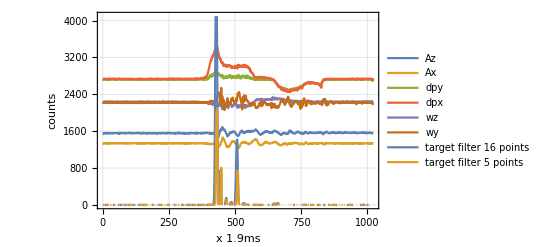

```mathematica
Show[raw,tf]
```

Make a function to do the cross-correlation

```mathematica
showfiletarget[file_,target_]:=Block[{},If[StringQ[file],datafile = file,datafile = SystemDialogInput["FileOpen"]];
Print[datafile];
filedata =Import[datafile];
lastrecord = Length[filedata];
d ={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]}&/@filedata;
npoints= Length[d];
t = Map[Part[#,1]&,d];
td = {MapThread[List,{t,Map[Part[#,2]&,d]}],MapThread[List,{t,Map[Part[#,3]&,d]}],MapThread[List,{t,Map[Part[#,4]&,d]}],MapThread[List,{t,Map[Part[#,5]&,d]}],MapThread[List,{t,Map[Part[#,6]&,d]}],MapThread[List,{t,Map[Part[#,7]&,d]}],MapThread[List,{t,Map[Part[#,8]&,d]}],MapThread[List,{t,Map[Part[#,9]&,d]}]};
corrA = ((#[[2]]-m[[2]]&/@d )(#[[3]]-m[[3]]&/@d) )/(sd[[2]] sd[[3]] );
corrW = ((#[[9]]-m[[9]]&/@d )(#[[8]]-m[[8]]&/@d ))/(sd[[9]] sd[[8]]);
corrP =((#[[6]]-m[[6]]&/@d )(#[[7]]-m[[7]]&/@d))/(sd[[6]] sd[[7]]);
corrAll=corrA corrW corrP;
crosscorr ={}; Do[cc=0;
(*20480 was added here, to keep scaling after removing npoints dependency from corrA, corrW, corrP*)
Do[cc = cc+ 20480target[[j]]*corrAll[[i+j]];,{j,1,16}];
AppendTo[crosscorr,cc],
{i,1,Length[corrAll]-Length[target]}];
GraphicsGrid[{{ListLinePlot[td,PlotLegends->{"Az","Ax","Ay","dpz","dpy","dpx","wz","wy"},Frame->True,PlotRange->{Automatic,{0,4096}},FrameLabel->{"x 1.9ms ","counts"},GridLines->Automatic,ImageSize->400]},{ListLinePlot[{npoints*corrA,npoints*corrW,npoints*corrP,crosscorr},PlotLegends->{"AzAx","WzWy","PxPy","target"},Frame->True,PlotRange->{-50,50},FrameLabel->{"x 1.9ms ","counts"},GridLines->Automatic,ImageSize->400]}},ImageSize->Large]]
```

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c20221215182.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215182.dat

-Graphics-

#### For DSP look at raw products

```mathematica
cA = ((#[[2]]-m[[2]]&/@d )(#[[3]]-m[[3]]&/@d) )/8;
cW = ((#[[9]]-m[[9]]&/@d )(#[[8]]-m[[8]]&/@d ))/8;
cP =((#[[6]]-m[[6]]&/@d )(#[[7]]-m[[7]]&/@d))/8;
{cA[[428]],cP[[428]],cW[[428]]}
```

{85.629,13575.1,-59.0652}

```mathematica
{cAP=cA[[428]]*cP[[428]]/8,cWT =cW[[428]]*-220/8}
```

{145303.,1624.29}

```mathematica
cAll =cAP*cWT/8
```

2.95018×10^7

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c20221215170.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215170.dat

-Graphics-

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212151614.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212151614.dat

-Graphics-

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c20221215155.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c20221215155.dat

-Graphics-

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212151356.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212151356.dat

-Graphics-

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212151243.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212151243.dat

-Graphics-

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212151049.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212151049.dat

-Graphics-

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c2022121536.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c2022121536.dat

-Graphics-

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c2022121501.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c2022121501.dat

-Graphics-

```mathematica
showfiletarget["C:\\Users\\Mike\\OneDrive\\FAERO\\FPGA\\innovateFPGA\\DE10-Nano\\DE10_NANO_SoC_GHRD\\hps\\data\\c202212145827.dat",target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202212145827.dat

-Graphics-

```mathematica
showfiletarget[0,target]
```

C:\Users\Mike\OneDrive\FAERO\FPGA\innovateFPGA\DE10-Nano\DE10_NANO_SoC_GHRD\hps\data\c202211321117.dat

-Graphics-